# Loading Initial Data

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse\3) Fitting Other Orders\Export

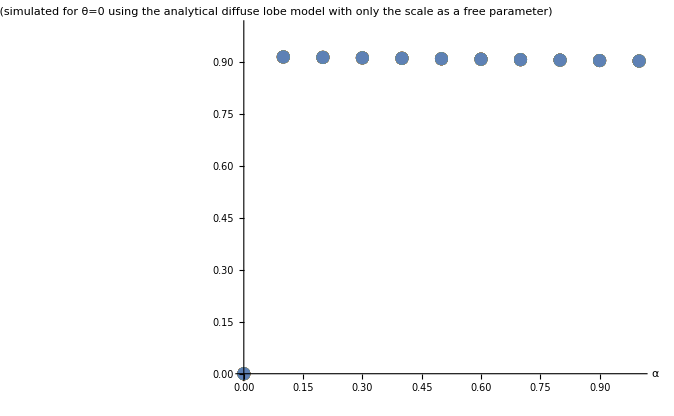

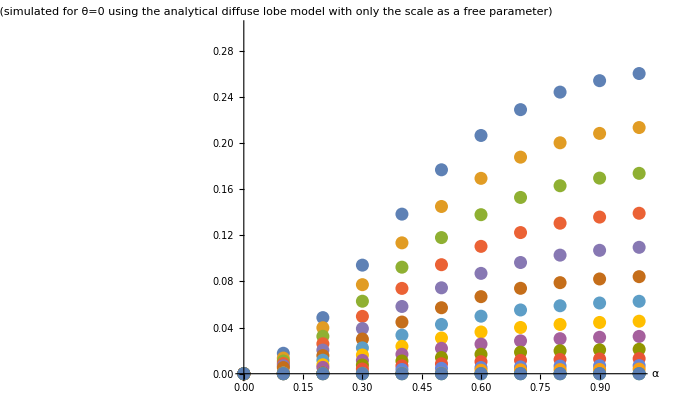

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
resX = 10;
resY=16;
albedoRawFiles = Table[{i},{i,1,resY}];
For[albedo=0,albedo<resY,albedo++,{
str=OpenRead["results_order3_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
albedoRawFiles[[1+albedo]]= Table[  rawFile[[j]], {j,1,resX}];
Close[str];
} ]
MatrixForm[albedoRawFiles];
albedoRawFiles[[1]];
(* Notice here we divide roughness by resX since we skipped simulating roughness at exactly 0 as we now know the lobe is 0 in size *)
roughnessParms = Table[Prepend[Table[{1-(i-1)/resX,albedoRawFiles[[j]][[i]][[2]]},{i,1,resX}],{0,0}],{j,1,resY}];
scaleParms = Table[Prepend[Table[{1-(i-1)/resX,albedoRawFiles[[j]][[i]][[3]]},{i,1,resX}],{0,0}],{j,1,resY}];
ListPlot[roughnessParms,PlotRange->{0,1.0},AxesLabel->{"α","16 albedos\n(simulated for θ=0 using the analytical diffuse\nlobe model with only the scale as a free parameter)"}]
ListPlot[scaleParms,PlotRange->{0,0.3},AxesLabel->{"α","16 albedos\n(simulated for θ=0 using the analytical diffuse\nlobe model with only the scale as a free parameter)"}]
```

### Choosing the Model

(a→-0.00602406 | b→0.252628 | c→0.390207 | d→-0.382049
a→-0.00527378 | b→0.207552 | c→0.32108 | d→-0.314493
a→-0.00430014 | b→0.168975 | c→0.261342 | d→-0.256012
a→-0.0033986 | b→0.133497 | c→0.213695 | d→-0.207695
a→-0.00267885 | b→0.105108 | c→0.168606 | d→-0.163827
a→-0.00205915 | b→0.0807077 | c→0.129595 | d→-0.125925
a→-0.0026447 | b→0.0615578 | c→0.100231 | d→-0.0979008
a→-0.0018998 | b→0.041617 | c→0.0803262 | d→-0.0757033
a→-0.00134863 | b→0.0295046 | c→0.057272 | d→-0.0539312
a→-0.00101507 | b→0.0118951 | c→0.0578695 | d→-0.0483489)

(-0.00602406+0.252628 u+0.390207 u^2-0.382049 u^3
-0.00527378+0.207552 u+0.32108 u^2-0.314493 u^3
-0.00430014+0.168975 u+0.261342 u^2-0.256012 u^3
-0.0033986+0.133497 u+0.213695 u^2-0.207695 u^3
-0.00267885+0.105108 u+0.168606 u^2-0.163827 u^3
-0.00205915+0.0807077 u+0.129595 u^2-0.125925 u^3
-0.0026447+0.0615578 u+0.100231 u^2-0.0979008 u^3
-0.0018998+0.041617 u+0.0803262 u^2-0.0757033 u^3
-0.00134863+0.0295046 u+0.057272 u^2-0.0539312 u^3
-0.00101507+0.0118951 u+0.0578695 u^2-0.0483489 u^3)

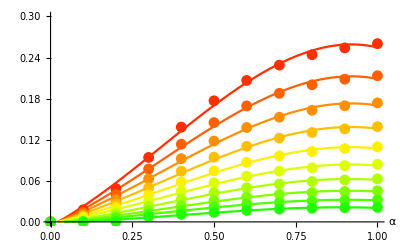

```mathematica
Clear[a,b,c,d]
modelS=a+b*u+c*u^2;
modelS=a + b*u+c*u^2+d*u^3;
fittingS = Table[FindFit[ scaleParms[[j]],modelS,{a,b,c,d},u ],{j,1,resX}];
MatrixForm[fittingS]
MatrixForm[modelS/.fittingS]
Show[
Table[Plot[modelS/.fittingS[[j]],{u,0,1},PlotRange->{0,0.3},PlotStyle->Hue[j/32],AxesLabel->{"α",}],{j,1,resX}],
Table[ListPlot[scaleParms[[j]],PlotRange->{0,0.3} ,PlotStyle->Hue[j/32],AxesLabel->{"α",}],{j,1,resX}]
]
```

## Using only the Curve for the Largest Albedo

-0.00602406+0.252628 α+0.390207 α^2-0.382049 α^3

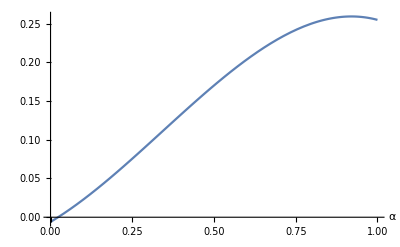

```mathematica
fS[α_]=Evaluate[modelS/.fittingS[[1]]/.u->α]
Plot[fS[α],{α,0,1},AxesLabel->{"α"}]
```

```mathematica
0.2104236647936169 α+0.47017202145255654 α^2-0.42647398758626226 α^3
```

0.210424 α+0.470172 α^2-0.426474 α^3

0.260281 is the largest amplitude we get for an order 3 lobe with albedo =1
To be compared to the 0.625075 amplitude we get for an order 2 lobe with albedo = 1

2.40154

-0.00379636+2.35119 α-2.79981 α^2+1.04001 α^3

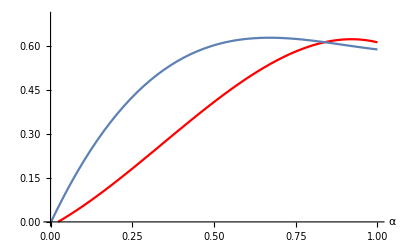

```mathematica
factor=0.6250752325886533/0.2602812531401859
fSorder2[α_]=-0.0037963602355835496+2.35118817316429 α-2.7998108086200135 α^2+1.0400142983433336 α^3
Show[
Plot[factor * fS[α],{α,0,1},AxesLabel->{"α"},PlotStyle->Red,PlotRange->{0,0.7}],
Plot[fSorder2[α],{α,0,1},AxesLabel->{"α"},PlotRange->{0,0.7}]
]
```

These are clearly not the same curve, they don’t depend on roughness α in the same way...

## Applying the same Function with Multiple Albedos

(amp→1.
amp→0.820004
amp→0.667467
amp→0.534331
amp→0.420965
amp→0.323287
amp→0.241086
amp→0.174517
amp→0.123996
amp→0.0805772
amp→0.0496788
amp→0.0258783
amp→0.0125939
amp→0.000423627
amp→4.80634×10^-6
amp→4.80634×10^-6)

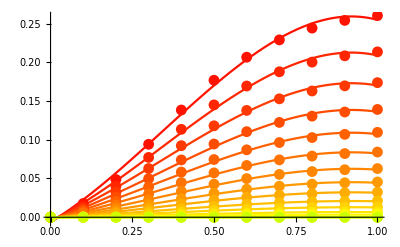

```mathematica
modelS2=amp*fS[u];
fittingS2 = Table[FindFit[ scaleParms[[albedo]],modelS2,{amp},u ],{albedo,1,resY}];
MatrixForm[fittingS2]
MatrixForm[modelS2/.fittingS2];
Show[
Table[Plot[modelS2/.fittingS2[[albedo]],{u,0,1},PlotStyle->Hue[albedo/80]], {albedo,1,resY}],
Table[ListPlot[scaleParms[[albedo]],PlotStyle->Hue[albedo/80]],{albedo,1,resY}]
]
```

## Retrieving the Amplitude Relationship

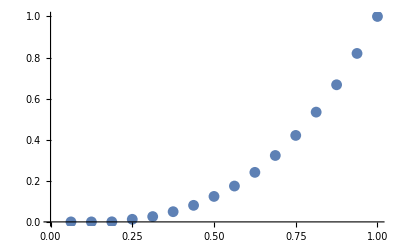

```mathematica
fitScaleParms = Table[{1-(albedo-1)/resY, Max[0,amp/.fittingS2[[albedo]]]},{albedo,1,resY}];
ListPlot[fitScaleParms,PlotRange->{0,1}]
```

{a→2.53861×10^-6,b→-0.0257491,c→0.0537561,d→0.969855}

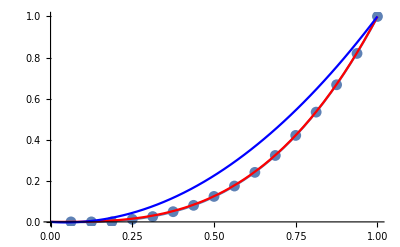

```mathematica
ampModel=a+b*u+c*u^2+d*u^3; (* Use a suspected 3rd order polynomial *)
fittingAmp = FindFit[fitScaleParms, ampModel, {a,b,c,d},u]

(* Manual override using these very simple parameters *)
fittingAmp2 = {a->0,b->0,c->0,d->1};

Show[
ListPlot[fitScaleParms,PlotRange->{0,1}],
Plot[ampModel/.fittingAmp,{u,0,1}],
Plot[ampModel/.fittingAmp2,{u,0,1},PlotStyle->Red],
Plot[0-0.1u+1.1 u^2,{u,0,1},PlotStyle->Blue]   (* Show order 2 curve in blue *)
]
```

Final Expression

We can now obtain the final expression for the function matching the lobe scale factor at order 3:

k(ρ) = 1 - 3 (1 - ρ) + 3 (1 - ρ)^2-(1-ρ)^3
k(ρ) = 0 - 0.05 ρ + 0.05 ρ^2 + ρ^3
σ(α, ρ) = k(ρ) [-0.00602406+0.252628 α+0.390207 α^2-0.382049 α^3]

```mathematica
k[ρ_] = ρ^3;
f[ μ_,α_,ρ_] = k[ρ] (-0.006024064722416875+0.25262765805538445 α+0.3902065605355212 α^2-0.3820487315212411 α^3);
Show[Table[Plot3D[f[μ,α,1-albedo/10],{μ,0,1},{α,0,1},AxesLabel->{"θ","α","lobe scale"},PlotStyle->GrayLevel[1-albedo/10]],{albedo,0,9}]]
```

-Graphics3D-